# Practical 5

### Submitted By- Puranjyoti Bera (20201043)

Show that the image of the right half plane Re(z) = x > 1 under the linear transformation w = (-1 + i)z - 2 + 3i is the half plane v > u + 7, where u = Re(w) etc. Plot the map.

The right half plane Re(z)= x > 1 is given by the figure

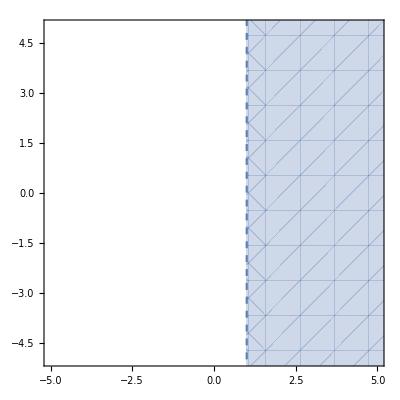

The image of the right half plane Re(z)= x > 1 under the function f(z)= (-2+3 ⅈ)-(1-ⅈ) z is v>7+u and is given by the figure

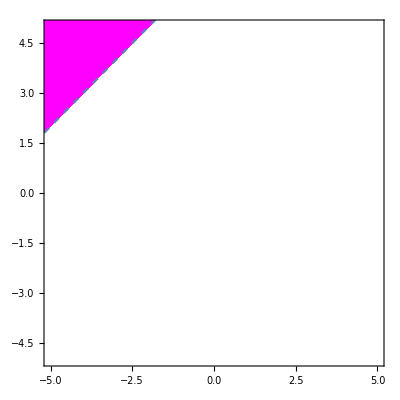

```mathematica
Print["The right half plane Re(z)= x > 1 is given by the figure"];
RegionPlot[Re[x+I*y]>1,{x,-10,10},{y,-10,10},BoundaryStyle->Dashed,PlotRange->5,Axes->True]
f[z_]:=(-1+I)*z-2+3*I;
w=u+I*v;
root:=z/.ComplexExpand[Solve[f[z]==w,z]]
Print["The image of the right half plane Re(z)= x > 1 under the function f(z)= ",f[z]," is ", Simplify[Refine[Re[root[[1]]]>1],Element[{u,v},Reals]], " and is given by the figure"];
RegionPlot[Re[root[[1]]]>1,{u,-10,10},{v,-10,10},PlotStyle->Magenta,BoundaryStyle->Dashed,PlotRange->5,Axes->True]
```